# Graph states on Rydberg neutral atoms

main ref : www.nature.com/articles/s41586-022-04592-6

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]*)
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink. Now it works as well directly using the default pre-compiled binary. But it usea only single core.

```mathematica
Import["~/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_gpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz
Length unit: μm

## 1D cluster state

```mathematica
el=Join[#<->#+1->1&/@Range[0,10,2],#<->#+1->2&/@Range[1,9,2]];
cluster=Graph[el//Keys,VertexSize->0.5,VertexStyle->Directive[White,EdgeForm[Thick]],BaseStyle->{17,FontFamily->"Serif"},ImageSize->900,EdgeStyle->Directive[Black,Thick],VertexLabels->Placed[Automatic,Center],EdgeLabels->el,EdgeLabelStyle->Directive[Background->White,Bold,Red]]
```

-Graphics-

-Graphics-

```mathematica
(* Expected value of each stabiliser S_j *)
stabcluster={0.8772585669781932,0.8274143302180685,0.887227414330218,0.8598130841121496,0.8772585669781932,0.8772585669781932,0.852336448598131,0.8722741433021808,0.8697819314641745,0.8722741433021808,0.8423676012461061,0.8897196261682243};
(* <S_j> on the noisy one *)
meancluster=0.87;
(*  <S_j> on ideal SPAM *)
sideal=0.91;
```

## The virtual device specification

```mathematica
Options[RydbergHub]={
(* The total number of physical qubits *)
qubitsNum-> 12,
(*Physical location on each qubit described with 2D-vector*)
AtomLocations-><|#->{#,0}&/@VertexList@cluster|>,
(* It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.5*10^6,
(* vacuum life time, where T1=τvac/N in μs *)
VacLifeTime->48*10^6,
(* Rabi frequency MHz *)
RabiFreq->1,
(* Asymmetric Bit-flip probability during single qubit operation *)
ProbBFRot-><|10->0.02, 01->0.03|>,
(* Unit lattice in μm. This will be the unit of the lattice/locations given in qubitLocations *)
UnitLattice->3,
(* blockade radius in μm*)
BlockadeRadius->1,
(* Leakage probability in the initalisation *)
ProbLeakInit->0.001,
(* Leakage induced by movements *)
ProbLeakMove->0.01,
(* duration on the initialization *)
DurInit->5*10^5,
(* measurement induces atom loss afterward *)
FidMeas-> 0.98,
DurMeas-> 10,
(* The increasing probability of atom loss on each measurement. The value keeps increasing until being initialised *)
ProbLossMeas-> 0.01,
(* leak probability of implementing multi-qubit gates *)
ProbLeakCZ-> <|01-> 0.006,11->0.001 |>
};
```

## Drawing

```mathematica
(*returns graph state stabilizer of a node*)
stabgs[graph_,node_]:=With[{neig=Complement[VertexList@NeighborhoodGraph[graph,node],{node}]},
ToExpression[StringRiffle[Join[{Subscript[X, node]},Subscript[Z, #]&/@neig]]]]
```

```mathematica
showgs[title_:"",opt_:{}]:=PlotAtoms[devGS,Sequence@@opt,ImageSize->900,ShowBlockade->Range[0,11],LabelStyle->Directive[17,Black],BaseStyle->{16,FontFamily->"Times"},PlotRange->{{-1,37},{-1.3,1.3}},Epilog->Inset[Style[title,{Red,Bold}],Scaled[{0.97,0.15}]],Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],
FrameTicks->{{{-1,0,1},None},{Automatic,None}}
];
```

```mathematica
circ1=CircRydbergHub[Flatten@{{Subscript[Init, #],Subscript[Ry, #][π/2]}&/@Range[0,11]},RydbergHub[],Parallel->True];
circ2={{Subscript[ShiftLoc, Range[1,11,2]][{-0.75,0}]}};
circ3={Subscript[C, #][Subscript[Z, #+1]]&/@Range[0,10,2]};
circ4={{Subscript[ShiftLoc, Range[1,11,2]][{1.5,0}]}};
circ5={Subscript[C, #][Subscript[Z, #+1]]&/@Range[1,9,2]};
```

```mathematica
devGS=RydbergHub[];
f1=showgs["initial",{ImagePadding->{{30,20},{0,0}}}];
noisycirc1=InsertCircuitNoise[circ1,devGS];
noisycirc2=InsertCircuitNoise[circ2,devGS];
f2=showgs["       1",{ImagePadding->{{30,20},{0,0}}}];
noisycirc3=InsertCircuitNoise[circ3,devGS];
noisycirc4=InsertCircuitNoise[circ4,devGS];
f3=showgs["       2",{ImagePadding->{{30,20},{20,0}}}];
noisycirc5=InsertCircuitNoise[circ5,devGS];
```

```mathematica
Column[{cluster,f1,f2,f3},Center,Spacings->0]
(*Export["~/vqd/img/rydberg_graph.pdf",%]*)
```

-Graphics-

## Setups

```mathematica
DestroyAllQuregs[];
ρ=CreateDensityQureg[12];
ρinit=CreateDensityQureg[12];
ρwork=CreateDensityQureg[12];
```

```mathematica
SetQuregMatrix[ρinit,RandomMixState[12]];
```

```mathematica
totalcirc=Join@@(ToExpression["circ"<>ToString@#]&/@Range[1,5])
```

{{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Init_6,Init_7,Init_8,Init_9,Init_10,Init_11},{Ry_0[π/2],Ry_1[π/2],Ry_2[π/2],Ry_3[π/2],Ry_4[π/2],Ry_5[π/2],Ry_6[π/2],Ry_7[π/2],Ry_8[π/2],Ry_9[π/2],Ry_10[π/2],Ry_11[π/2]},{ShiftLoc_{1,3,5,7,9,11}[{-0.75,0}]},{C_0[Z_1],C_2[Z_3],C_4[Z_5],C_6[Z_7],C_8[Z_9],C_10[Z_11]},{ShiftLoc_{1,3,5,7,9,11}[{1.5,0}]},{C_1[Z_2],C_3[Z_4],C_5[Z_6],C_7[Z_8],C_9[Z_10]}}

```mathematica
noisycirc=InsertCircuitNoise[totalcirc,RydbergHub[]];
(*Simplify, remove errors with zero-parameters *)
enoisycirc=DeleteElements[ExtractCircuit[noisycirc],{Subscript[Depol, __][0.],Subscript[Deph, __][0.]}];
```

Run the circuit without measurement. We start from an unknown mixed state

```mathematica
ApplyCircuit[CloneQureg[ρ,ρinit],enoisycirc]
```

{}

### [Quoted values] SPAM removal: 0.91, noisy: 0.87

#### Pulled from the density matrix

```mathematica
stabdata=CalcExpecPauliString[ρ,stabgs[cluster,#],ρwork]&/@Range[0,11]
Mean@stabdata
```

{0.91502,0.915066,0.915034,0.915069,0.915034,0.915069,0.915034,0.915069,0.915034,0.915069,0.915031,0.915059}

0.915049

#### Gather the statistics by shots

Note that the “X” measurement done in the circuit is flipped: H=Ry[π/2]X

```mathematica
CalcCircuitMatrix[{Subscript[Ry, 0][π/2],Subscript[X, 0]}]//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
DrawCircuit@{Subscript[Ry, 0][π/2],Subscript[X, 0]}
```

-Graphics-

```mathematica
CalcCircuitMatrix[Subscript[X, 0]].CalcCircuitMatrix[Subscript[Ry, 0][π/2]]
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
(*Two measurement settings: {Subscript[S, j]} where (1) j are even, (2) j are odd  
Put measurements at the very last!*)
evensm={Subscript[Ry, #][π/2]&/@Range[0,11,2],Subscript[M, #]&/@Range[0,11]};
oddsm={Subscript[Ry, #][π/2]&/@Range[1,11,2],Subscript[M, #]&/@Range[0,11]};
```

### The graph state simulation

```mathematica
ClearAll[SimulateGraphState]
SimulateGraphState[ρ_,ρinit_,ρwork_,ρstore_,nshots_,options_:{}]:=Module[{noisycirc,enoisycirc,emeasnoisy,omeasnoisy,statevenmeas={},statoddmeas={},scount,outeig,stabideal,totalcirc,chart,mean,ideal,cluster},
totalcirc={
{Subscript[Init, 0],Subscript[Init, 1],Subscript[Init, 2],Subscript[Init, 3],Subscript[Init, 4],Subscript[Init, 5],Subscript[Init, 6],Subscript[Init, 7],Subscript[Init, 8],Subscript[Init, 9],Subscript[Init, 10],Subscript[Init, 11]},{Subscript[Ry, 0][π/2],Subscript[Ry, 1][π/2],Subscript[Ry, 2][π/2],Subscript[Ry, 3][π/2],Subscript[Ry, 4][π/2],Subscript[Ry, 5][π/2],Subscript[Ry, 6][π/2],Subscript[Ry, 7][π/2],Subscript[Ry, 8][π/2],Subscript[Ry, 9][π/2],Subscript[Ry, 10][π/2],Subscript[Ry, 11][π/2]},{Subscript[ShiftLoc, {1,3,5,7,9,11}][{-0.75,0}]},{Subscript[C, 0][Subscript[Z, 1]],Subscript[C, 2][Subscript[Z, 3]],Subscript[C, 4][Subscript[Z, 5]],Subscript[C, 6][Subscript[Z, 7]],Subscript[C, 8][Subscript[Z, 9]],Subscript[C, 10][Subscript[Z, 11]]},{Subscript[ShiftLoc, {1,3,5,7,9,11}][{1.5,0}]},{Subscript[C, 1][Subscript[Z, 2]],Subscript[C, 3][Subscript[Z, 4]],Subscript[C, 5][Subscript[Z, 6]],Subscript[C, 7][Subscript[Z, 8]],Subscript[C, 9][Subscript[Z, 10]]}
};
cluster=Keys@Join[#<->#+1->1&/@Range[0,10,2],#<->#+1->2&/@Range[1,9,2]];
noisycirc=InsertCircuitNoise[totalcirc,RydbergHub[Sequence@@options]];
(*Simplify, remove errors with zero-parameters *)
     enoisycirc=DeleteElements[ExtractCircuit[noisycirc],{Subscript[Depol, __][0.],Subscript[Deph, __][0.]}];
ApplyCircuit[CloneQureg[ρ,ρinit],enoisycirc];
CloneQureg[ρstore,ρ];
emeasnoisy=ExtractCircuit@InsertCircuitNoise[evensm,RydbergHub[Sequence@@options]];
omeasnoisy=ExtractCircuit@InsertCircuitNoise[oddsm,RydbergHub[Sequence@@options]];

Table[
(* Note that this is okay because we don't have any function that depends on the absolute time.*)
(* even measurements*)
CloneQureg[ρ,ρstore];
AppendTo[statevenmeas,Flatten@ApplyCircuit[ρ,emeasnoisy]];
(* odd measurements*)
CloneQureg[ρ,ρstore];
AppendTo[statoddmeas,Flatten@ApplyCircuit[ρ,omeasnoisy]];
,{nshots}
];

(* stabilizer count *)
scount=Association@Table[j->0,{j,VertexList@cluster}];
(* First measurement setting: X,Z,X,Z...*)
Table[
outeig=Table[
If[EvenQ[k-1],
out[[k]]/.{0:>-1},(*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];
Table[
(* +1 - -1 *)
scount[node]+=Times@@(outeig[[#+1]]&/@VertexList[NeighborhoodGraph[cluster,node]]);
,{node,0,11,2}];
,{out,statevenmeas}];
(* Second measurement setting: Z,X,Z,X...*)
Table[
outeig=Table[
If[OddQ[k-1],
out[[k]]/.{0:>-1}, (*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];
Table[
scount[node]+=Times@@(outeig[[#+1]]&/@VertexList[NeighborhoodGraph[cluster,node]]);
,{node,1,11,2}];
,{out,statoddmeas}];
stabideal=CalcExpecPauliString[CloneQureg[ρ,ρstore],stabgs[cluster,#],ρwork]&/@Range[0,11];
mean=N@Mean@Values[scount/nshots];
ideal=Mean[stabideal];
<|"opt"->RydbergHub[Sequence@@options][OptionsUsed],"outeven"->statevenmeas,"outodd"->statoddmeas,"scount"->scount,"sideal"->stabideal|>
]
```

```mathematica
drawChart[res_,expresults_]:=With[{scount=res["scount"],nshots=res["outeven"]//Length,stabideal=res["sideal"]},
Show[
BarChart[Values@scount/nshots,ChartLabels->("S"<>ToString[#,TraditionalForm]&/@Range[0,11]),Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->1,ChartStyle->ColorData["Rainbow"][0.3],PlotRange->{Automatic,{0,1}}],
BarChart[expresults,ChartStyle->Directive[Opacity[0],EdgeForm[{Dashed,Thick}]]],
ListPlot[stabideal,Joined->True,PlotStyle->{Red,Thick,Dotted},PlotMarkers->{Red,7}],ImageSize->200,Background->White,LabelStyle->{16,FontFamily->"Serif"}
]
]

showResults[res_,expresults_]:=With[{dev=RydbergHub[Sequence@@res[["opt"]]],nshots=res["outeven"]//Length},
{dev[OptionsUsed],"shots="<>ToString@nshots,drawChart[res,expresults]}
]
```

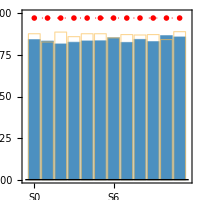
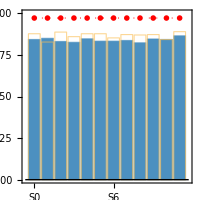
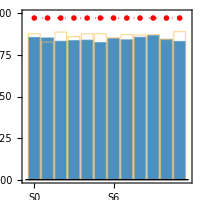
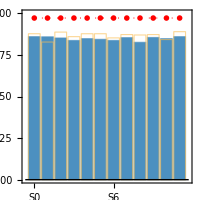
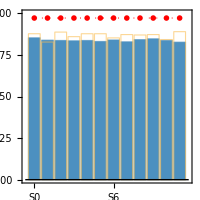
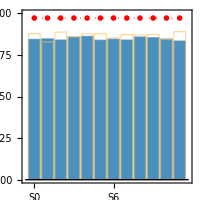
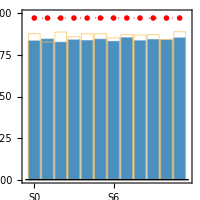
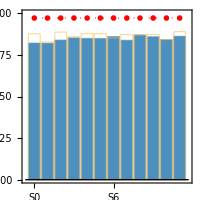

```mathematica
Last@showResults[#,stabcluster]&/@cluster1d
```

```mathematica
DestroyAllQuregs[];
{ρ,ρinit,ρwork,ρstore}=CreateDensityQuregs[12,4];
SetQuregMatrix[ρinit,RandomMixState[12]];
```

```mathematica
cluster1d[[1]]
```

```mathematica
show = {"hello there"}
Monitor[
 Table[
  res = SimulateGraphState[ρ, ρinit, ρwork, ρstore, nshots, {FidMeas -> 0.977}];
  AppendTo[cluster1d, res];
DumpSave["cluster1d.mx",cluster1d];
  show = showResults[res, stabcluster];
  , {nshots, {2000, 3000, 5000, 8000}}]
 , show[[-1]]]
```

{hello there}

{Null,Null,Null,Null}

```mathematica
show = {"hello there"}
nshots=10000
Monitor[
 Table[
  res = SimulateGraphState[ρ, ρinit, ρwork, ρstore, nshots, {FidMeas ->fm}];
  AppendTo[cluster1d, res];
DumpSave["cluster1d.mx",cluster1d];
  show = showResults[res, stabcluster];
  , {fm, {0.78,0.79}}]
 , show[[-1]]]
```

{hello there}

10000

{Null,Null}

```mathematica
show = {"hello there"}
nshots=8000
Monitor[
 Table[
  res = SimulateGraphState[ρ, ρinit, ρwork, ρstore, nshots, {FidMeas ->fm}];
  AppendTo[cluster1d, res];
DumpSave["cluster1d.mx",cluster1d];
  show = showResults[res, stabcluster];
  , {fm, {0.78,0.79}}]
 , show[[-1]]]
```

{hello there}

8000

{Null,Null}

## Steane code

-Graphics-

```mathematica
stabsteane={0.52,0.49,0.51,0.732,0.7,0.75};
logsteane={0.71,-0.02};
```

```mathematica
steaneres2[[1]]//Keys
```

Part::partd: Part specification steaneres2⟦1⟧ is longer than depth of object.

Keys::invrl: The argument steaneres2⟦1⟧ is not a valid Association or a list of rules.

Keys[steaneres2⟦1⟧]